```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\PEG8_Ag_PVP10\OA_Plates\more_PEG_small\equilibrate\1_NPT\TP_profile

```mathematica
log=OpenRead["thermo.lammps"]
```

InputStream[thermo.lammps,71]

```mathematica
Find[log,"# Step PotEng"]
```

# Step PotEng KinEng TotEng Temp Volume Press Lx Lz Pxx Pyy Pzz

```mathematica
thermo=Delete[ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],-1]
```

{{2000,-2530.36,900.705,-1629.65,«4»,48.3139,-201.412,297.324,399.18},«3958»}

```mathematica
Length[thermo]
```

3959

```mathematica
TimeSkip=1000;
```

```mathematica
Tavg=Mean[thermo[[All,5]]]
```

380.99

```mathematica
Tstd=StandardDeviation[thermo[[All,5]]]
```

2.31014

```mathematica
Tavg2=Mean[thermo[[TimeSkip;;Length[thermo],5]]]
```

380.963

```mathematica
Tstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],5]]]
```

2.30541

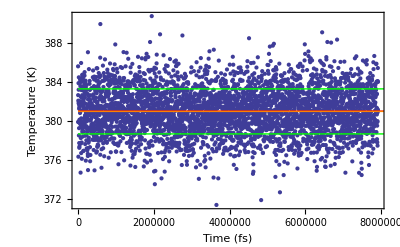

```mathematica
TGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]],thermo[[All,5]]],2]],Plot[{Tavg,Tavg2},{x,0,10000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Tavg2+Tstd2,Tavg2-Tstd2},{x,0,10000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Temperature (K)"}]
```

```mathematica
Pavg=Mean[thermo[[All,7]]]
```

3.71014

```mathematica
Pstd=StandardDeviation[thermo[[All,7]]]
```

514.486

```mathematica
Pavg2=Mean[thermo[[TimeSkip;;Length[thermo],7]]]
```

2.80995

```mathematica
Pstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],7]]]
```

515.684

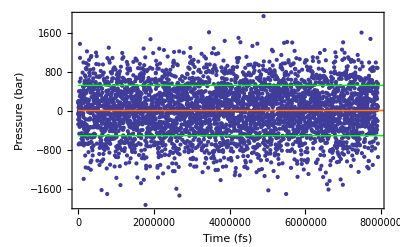

```mathematica
PGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]],thermo[[All,7]]],2]],Plot[{Pavg,Pavg2},{x,0,10000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Pavg2+Pstd2,Pavg2-Pstd2},{x,0,10000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Pressure (bar)"}]
```

```mathematica
Volavg=Mean[thermo[[All,6]]]
```

189207.

```mathematica
Volstd=StandardDeviation[thermo[[All,6]]]
```

14376.5

```mathematica
Volavg2=Mean[thermo[[TimeSkip;;Length[thermo],6]]]
```

188075.

```mathematica
Volstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],6]]]
```

642.106

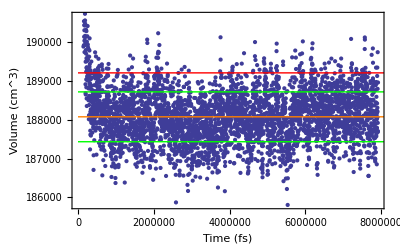

```mathematica
VGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]],thermo[[All,6]]],2]],Plot[{Volavg,Volavg2},{x,0,10000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Volavg2+Volstd2,Volavg2-Volstd2},{x,0,10000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Volume (cm^3)"}]
```

```mathematica
Engavg=Mean[thermo[[All,2]]]
```

-3136.23

```mathematica
Engstd=StandardDeviation[thermo[[All,2]]]
```

19.0519

```mathematica
Engavg2=Mean[thermo[[TimeSkip;;Length[thermo],2]]]
```

-3138.86

```mathematica
Engstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],2]]]
```

6.25807

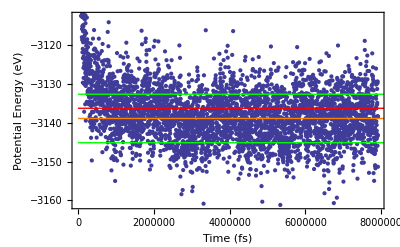

```mathematica
EGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]],thermo[[All,2]]],2]],Plot[{Engavg,Engavg2},{x,0,10000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Engavg2+Engstd2,Engavg2-Engstd2},{x,0,10000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Potential Energy (eV)"}]
```

```mathematica
CreateDirectory["graph"];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\PEG8_Ag_PVP10\\OA_Plates\\more_PEG_small\\equilibrate\\1_NPT\\TP_profile\\graph\\" already exists.

```mathematica
Export["graph/Tgraph.png",TGraph,ImageResolution->300];
Export["graph/Pgraph.png",PGraph,ImageResolution->300];
Export["graph/Vgraph.png",VGraph,ImageResolution->300];
Export["graph/Egraph.png",EGraph,ImageResolution->300];
```

```mathematica
Export["graph/report.txt",{"Tavg:",Tavg," ","Tstd:",Tstd," ","Pavg:",Pavg2," ","Pstd:",Pstd2," ","Volavg:",Volavg2," ","Volstd:",Volstd2," ","PotEngavg:",Engavg2," ","PotEngstd:",Engstd2}]
```

graph/report.txt